# Detecting nematic defects

```mathematica
ClearAll["Global`*"];
```

### Code

```mathematica
Clear[imageOrientationFn];
imageOrientationFn[image_,rad_]:=Block[{gy,gx,kernel1={1,0},kernel2={0,1},orientationParallel,orientationPerp},
gy=GaussianFilter[image,rad,kernel1];
gx=GaussianFilter[image,rad,kernel2];
orientationParallel=1/2 ArcTan[((gy*gy)-(gx*gx)),2(gx*gy)];
orientationPerp=ArcTan[Sin[orientationParallel],-Cos[orientationParallel]];
{orientationParallel,orientationPerp}
];
```

```mathematica
SetAttributes[makeVecs,HoldAll];
makeVecs[vals_,vecs_,s_,rQ_]:=With[{n=Length[vals]},If[TrueQ[rQ],Do[Switch[Sign[Im[vals[[k]]]],0,Null,1,vecs[[k]]+=s I vecs[[k+1]],-1,vecs[[k]]=Conjugate[vecs[[k-1]]]],{k,n}]]]
Options[getEigensystem]={Mode->Automatic};
getEigensystem[mat_?SquareMatrixQ,opts:OptionsPattern[]]:=Module[{m=mat,chk,ei,ev,lm,lv,n,rm,rQ,rv},
n=Length[mat];
Switch[OptionValue[Mode],
Right|Automatic,
{lm,rm}={"N","V"},
Left,{lm,rm}={"V","N"},
All,{lm,rm}={"V","V"},
_,{lm,rm}={"N","V"}];
LinearAlgebra`LAPACK`GEEV[lm,rm,m,ev,ei,lv,rv,chk,rQ];
If[!TrueQ[chk],
Message[getEigensystem::eivec0];
Return[$Failed,Module]
];
If[rQ,ev+=I ei];
Switch[OptionValue[Mode],Right|Automatic,rv=ConjugateTranspose[rv];
makeVecs[ev,rv,1,rQ];{ev,rv},Left,lv=ConjugateTranspose[lv];
makeVecs[ev,lv,-1,rQ];{ev,lv},All,{lv,rv}=ConjugateTranspose/@{lv,rv};
makeVecs[ev,rv,1,rQ];makeVecs[ev,lv,-1,rQ];
{ev,rv,lv},_,rv=ConjugateTranspose[rv];
makeVecs[ev,rv,1,rQ];{ev,rv}]
];
```

```mathematica
winNumberFn[{dimx_,dimy_},winsize_,overlap_]:={Floor[(dimx-overlap)/(winsize-overlap)],Floor[(dimy-overlap)/(winsize-overlap)]};
```

```mathematica
ClearAll[discretizeFn];
discretizeFn[data_,winsize_,overlap_]:=Block[{Nx,Ny,maxY,maxX,lsX,lsY},
{maxY,maxX}=If[Length[#]==2,#,Most@#]&@Dimensions[data];
{Nx,Ny}=winNumberFn[{maxX,maxY},winsize,overlap];
lsX=Range[1,Nx]*winsize-Range[0,Nx-1]*overlap - winsize/2;
lsY=Range[1,Ny]*winsize-Range[0,Ny-1]*overlap - winsize/2;
{lsX,lsY}
];
```

```mathematica
ClearAll[dataPartFn];
dataPartFn[imagedata_,winsize_,overlap_]:=Block[{lsX,lsY,minx,miny,part,maxY,maxX},
{lsX,lsY}=discretizeFn[imagedata,winsize,overlap];
{maxY,maxX}=Dimensions[imagedata];

part=Table[
minx=Max[Floor[lsX[[i]]-winsize/2],1];
miny=Max[Floor[lsY[[j]]-winsize/2],1];
{
{N@Mean@{minx,Floor[lsX[[i]]+winsize/2]},maxY-N@Mean@{miny,Floor[lsY[[j]]+winsize/2]} },
imagedata[[miny;;Floor[lsY[[j]]+winsize/2],minx;;Floor[lsX[[i]]+winsize/2]]]
},{j,Ny},{i,Nx}];
Flatten[part,1]ᵀ
];
```

```mathematica
directorFieldFn[imagedata_,winsize_,emptyCounts_]:=Block[{imgboxdata,zerocount,θ,Γ,Λ,Π,Q,αβ,eigvals,eigvecs},
ParallelTable[
imgboxdata=Flatten[part];
zerocount=Count[imgboxdata,0.];
θ=imgboxdata/. 0.->Nothing;
If[N[zerocount/winsize^2]100<=emptyCounts,
Subscript[Q, αβ]=∑_(p=1)^Length[θ] (Γ=θ[[p]];{Λ,Π}=N[{Cos[Γ],Sin[Γ]}];3/2({{Λ^2, Λ Π}, {Λ Π, Π^2}})-1/2({{1, 0}, {0, 1}}));
If[Subscript[Q, αβ]=!=0,
{eigvals,eigvecs}=Eigensystem[Subscript[Q, αβ]/Length[θ]];
First@Extract[eigvecs,Position[#,Max@#]&[Abs@eigvals]]
(*First@Extract[eigvecs,Position[eigvals,Max@eigvals]]*)
(*If[Abs[eigvals[[1]]]>=Abs[eigvals[[2]]],director=eigvecs[[1]]];
If[eigvals[[2]]>=eigvals[[1]],director=eigvecs[[2]]];
director*),
Null],
Null],{part,imagedata}]/.Null->{Null,Null}
]
```

```mathematica
ClearAll[fnComp,JFn];
(*JFn[OrderlessPatternSequence[{Null,Null},{Null,Null}]|OrderlessPatternSequence[{__Real},{Null,Null}]]:=None;*)
JFn[{Null,Null},{Null,Null}]:=None;
JFn[{__Real},{Null,Null}]:=None;
JFn[{Null,Null},{__Real}]:=None;

Block[{v1,v2,m,ang},
fnComp=Compile[{{vec1,_Real,1},{vec2,_Real,1}},
v1=vec1;v2=vec2;
ang=ArcTan[v1.v2,Abs[Det[{v1,v2}]]];
If[ang>N[π/2],v2*=-1];
m=Det[{v1,v2}];
ang=Sign[m] ArcTan[v1.v2,Abs[m]],
RuntimeOptions->"Speed",CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True}
]
]

JFn[x:{__Real}..]:=fnComp[x];

meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]};

If[$KernelCount==0,LaunchKernels[]]
```

CompiledFunction[…]

{Local,Local,Local,Local,Local,Local}

### Inputs

```mathematica
image=-Graphics-;mask=-Graphics-;orientationparallel=-Graphics-;
```

```mathematica
(*image=ImageTrim[image,{{1,52},{960,930}}];mask=ImageTrim[mask,{{1,52},{960,930}}];orientationparallel=ImageTrim[orientationparallel,{{1,52},{960,930}}];*)
```

```mathematica
winsize=100;
overlap=60;
emptyCounts=80;
colAssoc=<|0->GrayLevel[0],1/2->RGBColor[0, 0, 1],-1/2->RGBColor[1, 0, 0],-1->RGBColor[1, 0.5, 0],1->RGBColor[0, 1, 0]|>;
```

### Field Directors

```mathematica
{dimx,dimy}=ImageDimensions[image]; (*{dimy,dimx}=Dimension[ImageData@image]*)
{Nx,Ny}=winNumberFn[{dimx,dimy},winsize,overlap]; (*Nx are discretization in x-axis or kind of columns and Ny are discretizations in y-axis or kind of rows*)
{midPtsWins,imagedata}=dataPartFn[ImageData[orientationparallel*mask],winsize,overlap];
directorfield=directorFieldFn[imagedata,winsize,emptyCounts];
```

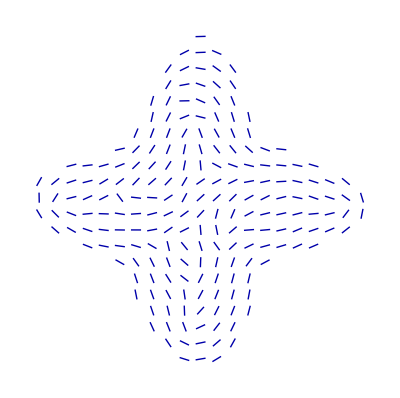

-Graphics-

```mathematica
directorScale=winsize/8;
Graphics[{Darker@Blue,MapThread[If[#==={0,0},Nothing,Line[{#2+directorScale*#1,#2-directorScale*#1}]]&,{directorfield/.Null->0,midPtsWins}]}]
(*note: midPtsWins have been computed in image coordinate system here*)
HighlightImage[image,{Red,Thickness[0.004],MapThread[If[#==={0.,0.},Nothing,Line[{#2+directorScale*#1,#2-directorScale*#1}]]&,{directorfield/.Null->0.,midPtsWins}]},ImageSize->Medium]
```

### Winding Number

```mathematica
Partition[directorfield,Nx]===ArrayReshape[directorfield,{Ny,Nx,2}]
parts=ArrayReshape[directorfield,{Ny,Nx,2}](*Partition[directorfield,Nx]*); 
(*Nx represents the number of columns you need the directorfield to be divided into .. ofcourse appropriate rownumbers will be generated .. same as ArrayReshape[directorfield,{Ny,Nx,2}]*)
```

True

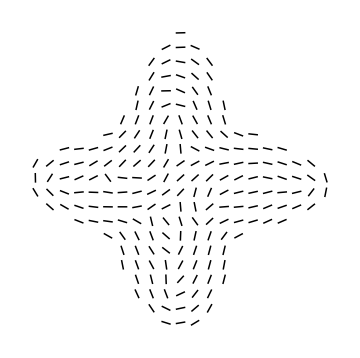

```mathematica
arr=Array[{##}&,{Ny,Nx}];
assoc=<|Rule@@@Flatten[{arr,parts},{3,2}]|>;
keys=Keys[assoc];
Graphics[{Thickness[0.003],KeyValueMap[If[#2=={0,0},Nothing,Line[{{#1[[2]],Ny+1-#1[[1]]}+1/3#2,{#1[[2]],Ny+1-#1[[1]]}-1/3#2}]]&,assoc/.Null->0]},ImageSize->Medium]
```

```mathematica
keystrunc=DeleteCases[keys,{1|Ny,_}|{_,1|Nx}];
neighbours={{0,1},{0,-1},{-1,0},{1,0},{-1,1},{-1,-1},{1,1},{1,-1}};
neighbourparts={{neighbours[[1]],neighbours[[5]]},{neighbours[[5]],neighbours[[3]]},{neighbours[[3]],neighbours[[6]]},{neighbours[[6]],neighbours[[2]]},{neighbours[[2]],neighbours[[8]]},{neighbours[[8]],neighbours[[4]]},
{neighbours[[4]],neighbours[[7]]},{neighbours[[7]],neighbours[[1]]}};
keypairings=Map[keystrunc[[10]]+#&,neighbourparts,{2}];
Graphics[{{PointSize[0.03],Blue,Point@keys,Lighter@Green,Point@keystrunc},Black,Thick,Arrowheads[Medium],Arrow[BSplineCurve[DeleteDuplicates[Flatten[keypairings,1]]~Join~{keypairings[[1,1]]}]]},ImageSize->Small,Background->LightGreen]//Rasterize[#,"Image",ImageSize->250]& (*the plot is tilted ... horizontal is y and vertical is x*)
```

-Graphics-

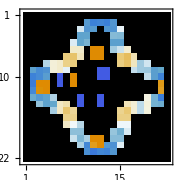

```mathematica
table=Table[
keypairings=Map[i+#&,neighbourparts,{2}];
Lookup[assoc,#]&/@keypairings,{i,keystrunc}];

chargeArr=Rationalize[Chop@Total[Transpose[JFn@@@#&/@table]/.None->0]/(2π)];

chargeArrtranspose=ArrayPad[Transpose@ArrayReshape[chargeArr,{Nx-2,Ny-2}],1];
MatrixPlot[chargeArrtranspose,ColorRules->{0->GrayLevel[0]},ImageSize->Small]
```

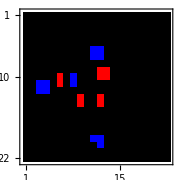

```mathematica
ϵ=0.05;
chargeArrtranspose=Replace[chargeArrtranspose,{x_/;N[1/2-ϵ]<=x<=N[1/2+ϵ]->1/2,x_/;N[-1/2-ϵ]<=x<=N[-1/2+ϵ]->-1/2},{2}];
chargeArrtranspose=Replace[chargeArrtranspose,Except[1/2|-1/2|1|-1]->0,{2}] ;
MatrixPlot[chargeArrtranspose,ColorRules->Thread[Keys@colAssoc->Values@colAssoc],ImageSize->Small]
```

```mathematica
arrmasks=SparseArray@MorphologicalComponents[ArrayComponents[chargeArrtranspose],CornerNeighbors->False];
posdefects=Mean@Extract[ArrayReshape[midPtsWins,Dimensions[chargeArrtranspose]~Join~{2}],Position[Normal@arrmasks,#]]&/@Union@arrmasks["NonzeroValues"];
postype=Mean@Extract[chargeArrtranspose,Position[Normal@arrmasks,#]]&/@Union@arrmasks["NonzeroValues"];
```

```mathematica
directorfieldP=directorfield/. {Null,Null}->{0,0};
GraphicsGrid[
{{
Rasterize[HighlightImage[image,MapThread[If[#1=!={0,0},{colAssoc[#3],Thickness[0.004],Line[{#2+winsize/8#1,#2-winsize/8#1}]}]&,{directorfieldP,midPtsWins,Flatten[chargeArrtranspose]}],ImageSize->Medium],"Image",ImageSize->1024]
,
Rasterize[HighlightImage[image,
{MapThread[If[#1=!={0,0},{colAssoc[#3],Thickness[0.004],Line[{#2+winsize/8#1,#2-winsize/8#1}]}]&,{directorfieldP,midPtsWins,Flatten[chargeArrtranspose]}],
MapThread[{colAssoc[#2],Point[#1]}&,{posdefects,postype}]},ImageSize->Medium],"Image",ImageSize->1024]
}}
]
```

-Graphics-

#### computing winding number from nematic angles

```mathematica
(*we can also compute the charge array using directly the angles rather than the JFn function that deals with directors*)
```

```mathematica
directorToAngle[{Null,Null}]:=None;
directorToAngle[director_]:=ArcTan[director[[-1]]/director[[1]]];
```

```mathematica
nemAngles=Map[directorToAngle,parts,{2}]/.x_?NumericQ:>-x;
```

```mathematica
assoc2=<|Rule@@@Flatten[{arr,nemAngles},{3,2}]|>;
keys2=Keys[assoc2];
keystrunc2=DeleteCases[keys2,{1|Ny,_}|{_,1|Nx}];
```

```mathematica
table2=Table[
keypairings=Map[(i+#)&,neighbourparts,{2}];
assoc2[#]&/@keypairings[[All,1]],{i,keystrunc2}];
```

```mathematica
table2=table2/.x_?(Count[#,None]>1&):>ConstantArray[None,8]; (* the parameter 1 can be changed so that charges are not calculated specifically with lots of NaNs*)
```

```mathematica
chargeArr2=Map[Total][Differences@*Reverse@*(Append[#,#[[1]]]&)/@(table2/.None->0)/.{x_/;-π/2<=x<=π/2:>0,x_/;x<-π/2:>π,x_/;x>π/2:>-π} ]/(2π);
```

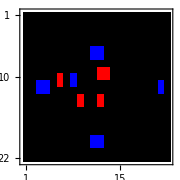

```mathematica
chargeArrtranspose2=ArrayPad[Transpose@ArrayReshape[chargeArr2,{Nx-2,Ny-2}],1];
MatrixPlot[chargeArrtranspose2,ColorRules->Thread[Keys@colAssoc->Values@colAssoc],ImageSize->Small]
```

```mathematica
arrmasks2=SparseArray@MorphologicalComponents[ArrayComponents[chargeArrtranspose2],CornerNeighbors->False];
posdefects2=Mean@Extract[ArrayReshape[midPtsWins,Dimensions[chargeArrtranspose2]~Join~{2}],Position[Normal@arrmasks2,#]]&/@Union@arrmasks2["NonzeroValues"];
postype2=Mean@Extract[chargeArrtranspose2,Position[Normal@arrmasks2,#]]&/@Union@arrmasks2["NonzeroValues"];
```

```mathematica
directorfieldP=directorfield/. {Null,Null}->{0,0};
HighlightImage[image,MapThread[If[#1=!={0,0},{colAssoc[#3],Thickness[0.004],Line[{#2+winsize/8#1,#2-winsize/8#1}]}]&,{directorfieldP,midPtsWins,Flatten[chargeArrtranspose2]}],ImageSize->Medium]
```

-Graphics-

```mathematica
HighlightImage[image,
{MapThread[If[#1=!={0,0},{colAssoc[#3],Thickness[0.004],Line[{#2+winsize/8#1,#2-winsize/8#1}]}]&,{directorfieldP,midPtsWins,Flatten[chargeArrtranspose2]}],
MapThread[{colAssoc[#2],Point[#1]}&,{posdefects2,postype2}]},ImageSize->Medium]
```

-Graphics-

### Winding number (subsampled)

```mathematica
Clear@dataPartFn2;
dataPartFn2[data_,{lsX_,lsY_},winsize_,translation_,dimx_,dimy_]:=Block[{Nx,Ny,maxXDir,maxYDir,rightX,leftX,rightY,leftY,overlap,part,midpt,indices},
overlap=winsize-translation;
{maxYDir,maxXDir}=Most@Dimensions[data];
{Nx,Ny}=winNumberFn[{maxXDir,maxYDir},winsize,overlap];
Print[{Nx,Ny}];
part=Table[
rightX=i(winsize)-(i-1)overlap;
leftX=rightX-translation;
rightY=j(winsize)-(j-1)overlap;
leftY=rightY-translation;
midpt=Mean/@{lsX[[{leftX,rightX}]],dimy-lsY[[{leftY,rightY}]]};
indices=Mean/@{{leftY,rightY},{leftX,rightX}};
{midpt,indices},
{j,Ny},{i,Nx}
];

{{Nx,Ny},part[[All,All,1]],part[[All,All,-1]]}
];
```

```mathematica
{lsX,lsY}=discretizeFn[ImageData[orientationparallel],winsize,overlap];
{maxYDir,maxXDir}=Most@Dimensions[parts];
windowBox=3;
translateBox=2;
overlapWin=windowBox-translateBox;
```

```mathematica
{{Nx2,Ny2},midpts,ls}=dataPartFn2[parts,{lsX,lsY},windowBox,translateBox,dimx,dimy]; (*Nx2 are discretization in x-axis or kind of columns and Ny2 are discretizations in y-axis or kind of rows*)
ls=Flatten[ls,1];
```

{10,10}

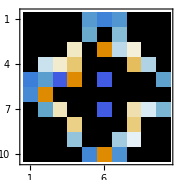

```mathematica
tablesubsampled=Table[
keypairings=Map[i+#&,neighbourparts,{2}];
Lookup[assoc,#]&/@keypairings,{i,ls}];
chargeArrSampled=Rationalize[Chop@Total[Transpose[JFn@@@#&/@tablesubsampled]/.None->0]/(2π)];
chargeArrtransposeSampled=ArrayReshape[chargeArrSampled,{Ny2,Nx2}];(*Partition[chargeArrSampled,Nx2]*)
MatrixPlot[chargeArrtransposeSampled,ColorRules->{0->GrayLevel[0]},ImageSize->Small]
```

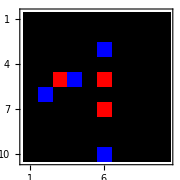

```mathematica
ϵ=0.05;
chargeArrtransposeSampled=Replace[chargeArrtransposeSampled,{x_/;N[1/2-ϵ]<=x<=N[1/2+ϵ]->1/2,x_/;N[-1/2-ϵ]<=x<=N[-1/2+ϵ]->-1/2},{2}];
chargeArrtransposeSampled=Replace[chargeArrtransposeSampled,Except[1/2|-1/2|1|-1]->0,{2}] ;
MatrixPlot[chargeArrtransposeSampled,ColorRules->Thread[Keys@colAssoc->Values@colAssoc],ImageSize->Small]
```

```mathematica
directorfieldP=directorfield/. {Null,Null}->{0,0};
HighlightImage[image,
{Black,Thickness[0.003],MapThread[If[#1==={0,0},Nothing,Line[{#2+winsize/8#1,#2-winsize/8#1}]]&,{directorfieldP,midPtsWins}],
MapThread[If[#1=={0,0}||#3==0,Nothing,{colAssoc[#3],Line[{#2+winsize/8#1,#2-winsize/8#1}]}]&,{directorfieldP,midPtsWins,Flatten[chargeArrtranspose]}],
PointSize[0.015],MapThread[If[#2==0,Nothing,{colAssoc[#2],Point[#1]}]&,{Flatten[midpts,1],Flatten[chargeArrtransposeSampled]}]},ImageSize->Medium]
```

-Graphics-

#### computing winding number from nematic angles (subsampled)

```mathematica
(*we can also compute the charge array using directly the angles rather than the JFn function that deals with directors*)
```

```mathematica
tablesubsampled2=Table[keypairings=Map[i+#&,neighbourparts,{2}];
assoc2[#]&/@keypairings[[All,1]],{i,ls}];
```

```mathematica
tablesubsampled2=tablesubsampled2/.x_?(Count[#,None]>1&):>ConstantArray[None,8]; (* the parameter 1 can be changed so that charges are not calculated specifically with lots of NaNs*)
```

```mathematica
chargeArrsubsampled2=Map[Total][Differences@*Reverse@*(Append[#,#[[1]]]&)/@(tablesubsampled2/.None->0)/.{x_/;-π/2<=x<=π/2:>0,x_/;x<-π/2:>π,x_/;x>π/2:>-π} ]/(2π);
```

```mathematica
chargeArrsubsampledtranspose2=ArrayReshape[chargeArrsubsampled2,{Ny2,Nx2}];
MatrixPlot[chargeArrsubsampledtranspose2,ColorRules->Thread[Keys@colAssoc->Values@colAssoc],ImageSize->Small]
```

-Graphics-

```mathematica
directorfieldP=directorfield/. {Null,Null}->{0,0};
HighlightImage[image,
{Black,Thickness[0.003],MapThread[If[#1==={0,0},Nothing,Line[{#2+winsize/8#1,#2-winsize/8#1}]]&,{directorfieldP,midPtsWins}],
MapThread[If[#1=={0,0}||#3==0,Nothing,{colAssoc[#3],Line[{#2+winsize/8#1,#2-winsize/8#1}]}]&,{directorfieldP,midPtsWins,Flatten[chargeArrtranspose]}],
PointSize[0.015],MapThread[If[#2==0,Nothing,{colAssoc[#2],Point[#1]}]&,{Flatten[midpts,1],Flatten[chargeArrsubsampledtranspose2]}]
},ImageSize->Medium]
```

-Graphics-

### Defect Annihilation

```mathematica
(*if two opposite defects are in close proximity they should annihilate*)
```

```mathematica
ClearAll[annihateDefectFn];
annihateDefectFn[chargedarr_,midpts_,thresh_:80]:=Block[{defectlocAssoc,distmat,pos,loc,chArr=chargedarr,u,v,$u,Fn},
Fn[$u_,t_,pts_]:=(
{u,v}={defectlocAssoc[$u],defectlocAssoc[-$u]};
If[Head[u]=!=Missing||Head[v]=!=Missing,
distmat=DistanceMatrix[N[u],N[v]];
While[Min[distmat]<=t &&Length[distmat]>1,
pos=FirstPosition[distmat,Min@distmat];
loc=Position[pts,Alternatives@@{u[[pos[[1]]]],v[[pos[[2]]]]}];
(chArr[[#[[1]],#[[-1]]]]=0)&/@loc;
u=Delete[u,pos[[1]]];
v=Delete[v,pos[[2]]];
distmat=DistanceMatrix[N[u],N[v]];
],
Echo["defect pair +"<>ToString[$u]<>" & "<>ToString[-$u]<>" do not exist"];
]
);
defectlocAssoc=KeyDrop[GroupBy[Flatten[{chargedarr,midpts},{2,3}],First->Last],0];
Fn[1/2,thresh,midpts];
Fn[1,thresh,midpts];
chArr
];
```

```mathematica
(*remove defects within a certain threshold distance*)
```

defect pair +1 & -1 do not exist

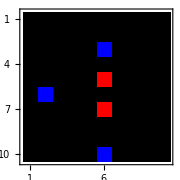

```mathematica
MatrixPlot[annihateDefectFn[chargeArrsubsampledtranspose2,midpts,80],ColorRules->Thread[Keys@colAssoc->Values@colAssoc],ImageSize->Small]
```

### Defect Stability

```mathematica
(* if defect is located in multiple frames, at least two frames. below i make an artificial data for 5 frames*)
```

```mathematica
res=annihateDefectFn[chargeArrsubsampledtranspose2,midpts,80];
```

defect pair +1 & -1 do not exist

```mathematica
madeupframes=Flatten[{chargeArrsubsampledtranspose2,res,Reverse[chargeArrsubsampledtranspose2],Reverse[res],res},{2,3}];
madeupframes[[6,{2,4}]]=1/2;
```

```mathematica
Grid[Transpose[madeupframes],Background->White,Dividers->{All, False}]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0

```mathematica
chargeStabilityFn[arrays_]:=Block[{defectbreakdown,defectbreakdownFrameNum,chArr=arrays,defpos,temp,stableduration},
defectbreakdown=Apply[Thread@*Rule]/@Transpose[{Flatten@*Map[Union]@*Split/@chArr,Map[Length]@*Split/@chArr},1<->2];
defectbreakdownFrameNum=Map[Thread[Keys[#]->Accumulate@Values@#]&,defectbreakdown];
temp=Position[defectbreakdown,1/2->1]~Join~Position[defectbreakdown,-1/2->1];(*the first indices represent position where unstable defects are located. defects that only appear in a single frame*)
defpos=Thread[{temp[[All,1]],Values@Extract[defectbreakdownFrameNum,temp]}];
Do[chArr[[i[[1]],i[[-1]]]]=Style[chArr[[i[[1]],i[[-1]]]],Bold,Blue,Background->LightRed],{i,defpos}];

temp=Position[defectbreakdown,1/2->x_/;x>1]~Join~Position[defectbreakdown,-1/2->x_/;x>1];(*position where stable defects are located*)
stableduration=Cases[defectbreakdown,PatternSequence[1/2->x_/;x>1],{2}]~Join~Cases[defectbreakdown,PatternSequence[-1/2->x_/;x>1],{2}]//Values;
defpos=Thread[{temp[[All,1]],Values[Extract[defectbreakdownFrameNum,temp]]}];
defpos=defpos~Join~Flatten[MapThread[Thread[{#[[1]],#[[2]]-Range[#2]+1}]&,{defpos,stableduration}],1];
Do[chArr[[i[[1]],i[[-1]]]]=Style[chArr[[i[[1]],i[[-1]]]],Bold,Blue,Background->LightBlue],{i,defpos}];
Transpose[chArr]
];
```

```mathematica
Grid[chargeStabilityFn@madeupframes,Background->White,Dividers->{All, False}]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0

```mathematica
Grid[Prepend[Prepend[chargeStabilityFn@madeupframes,Style[#,Magenta]&/@Range[Length@madeupframes]]ᵀ,Prepend[Style[ToExpression["t"<>ToString[#]],Magenta]&/@Range[Length[madeupframesᵀ]],("pos")/("time")]]ᵀ,Dividers->{{1,2},All}]
```

pos/time | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100
t1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
t2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
t3 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
t4 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
t5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0

### Defect Directionality (not important but a nice have to function)